## Direct Derivation of the Dynamic Regressor for a Stanford Arm examples of the theoretical results presented in: "Explicit Lagrangian Formulation of the Dynamic Regressors for Serial Manipulators", M. Gabiccini, A. Bracci, D. De Carli, M. Fredianelli, A. Bicchi submitted to the 2009 IEEE International Conference on Robotics and Automation (ICRA2009) to be held in Kobe, Japan, May 12 - 17, 2009

### Package

```mathematica
<<ScrewCalculusPro`ScrewCalculusPro`
<<ToMatlab`ToMatlab`
```

### UR10e Manipulator - definition of required quantities

Denavit-Hartenberg table with joint types added in the last slot [REQUIRED FOR DIRECT REGRESSOR CALCULATION]

```mathematica
tableUR10e[q1_,q2_,q3_,q4_,q5_,q6_]={
{0,            -Pi/2, 0.1273,q1,"R"},
{0.6120,    0        , 0.220941,q2,"R"},
{0.5723,    0        ,-0.1719,q3,"R"},
{0,            -Pi/2, 0.1149,q4,"R"},
{0,               Pi/2 ,0.1157,q5,"R"},
{0,               0         , 0.0922,q6,"R"}
}
```

{{0,-π/2,0.1273,q1,R},{0.612,0,0.220941,q2,R},{0.5723,0,-0.1719,q3,R},{0,-π/2,0.1149,q4,R},{0,π/2,0.1157,q5,R},{0,0,0.0922,q6,R}}

Symbolic variable definition [REQUIRED FOR DIRECT REGRESSOR CALCULATION]

```mathematica
qsym={q1,q2,q3,q4,q5,q6}
```

{q1,q2,q3,q4,q5,q6}

List of CGi's position vectors with respect to the local D-H frames [NOT REQUIRED FOR DIRECT REGRESSOR CALCULATION]

```mathematica
CGtableUR10e=Table[ToExpression[{"a"<>ToString[i],"b"<>ToString[i],"c"<>ToString[i]}],{i,1,Length[tableUR10e@@qsym]}]
```

{{a1,b1,c1},{a2,b2,c2},{a3,b3,c3},{a4,b4,c4},{a5,b5,c5},{a6,b6,c6}}

```mathematica
CGtableUR10e ={{0,0,0},
{-0.3060,0,0},
{-0.28615,0,0},
{0,0.1719,0},
{0,-0.1149,0},
{0,0,-0.0922}}
```

{{0,0,0},{-0.306,0,0},{-0.28615,0,0},{0,0.1719,0},{0,-0.1149,0},{0,0,-0.0922}}

List of inertia matrices with respect to the local CGi's [NOT REQUIRED FOR DIRECT REGRESSOR CALCULATION]

```mathematica
tensorlist=Table[ToExpression[{
{"I"<>ToString[i]<>"xx","-I"<>ToString[i]<>"xy","-I"<>ToString[i]<>"xz"},
{"-I"<>ToString[i]<>"xy","I"<>ToString[i]<>"yy","-I"<>ToString[i]<>"yz"},
{"-I"<>ToString[i]<>"xz","-I"<>ToString[i]<>"yz","I"<>ToString[i]<>"zz"}
}],{i,1,Length[tableUR10e@@qsym]}]
```

{{{I1xx,-I1xy,-I1xz},{-I1xy,I1yy,-I1yz},{-I1xz,-I1yz,I1zz}},{{I2xx,-I2xy,-I2xz},{-I2xy,I2yy,-I2yz},{-I2xz,-I2yz,I2zz}},{{I3xx,-I3xy,-I3xz},{-I3xy,I3yy,-I3yz},{-I3xz,-I3yz,I3zz}},{{I4xx,-I4xy,-I4xz},{-I4xy,I4yy,-I4yz},{-I4xz,-I4yz,I4zz}},{{I5xx,-I5xy,-I5xz},{-I5xy,I5yy,-I5yz},{-I5xz,-I5yz,I5zz}},{{I6xx,-I6xy,-I6xz},{-I6xy,I6yy,-I6yz},{-I6xz,-I6yz,I6zz}}}

```mathematica
tensorlist ={{{0,0,0},{0,0,0},{0,0,0}},
{{0,0,0},{0,0,0},{0,0,0}},
{{0,0,0},{0,0,0},{0,0,0}},
{{0,0,0},{0,0,0},{0,0,0}},
{{0,0,0},{0,0,0},{0,0,0}},
{{0,0,0},{0,0,0},{0,0,0}}}
```

{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
(*tensorlist ={{{0.031474312576900,0,0},{0,0.031474312576900,0},{0,0,0.021875625000000}},
{{0.036365625000000,0,0},{0,1.632467283798000,0},{0,0,1.632467283798000}},
{{0.010884375000000,0,0},{0,0.427952347172000,0},{0,0,0.427952347172000}},
{{0.005108247956700,0,0},{0,0.005512500000000,0},{0,0,0.005108247956700}},
{{0.005108247956700,0,0},{0,0.005108247956700,0},{0,0.005512500000000,0}},
{{0.0005264622894150000,0,0},{0,0.0005681250000000000,0},{0,0,0.0005264622894150000}}}*)
```

Extract just the first...

```mathematica
tensorlist[[1]]//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

List of link masses [NOT REQUIRED FOR DIRECT REGRESSOR CALCULATION]

```mathematica
masslist=Table[ToExpression["m"<>ToString[i]],{i,1,Length[tableUR10e@@qsym]}]
```

{m1,m2,m3,m4,m5,m6}

```mathematica
masslist = {7.778,12.93,3.87,1.96,1.96,0.2020}
```

{7.778,12.93,3.87,1.96,1.96,0.202}

### Time dependent variable definitions [ALL REQUIRED]

Version time dependent, configuration

```mathematica
q[t_]=Map[ToExpression[ToString[#]<>"[t]"]&,qsym]
```

{q1[t],q2[t],q3[t],q4[t],q5[t],q6[t]}

Velocity

```mathematica
qp[t_]=D[q[t],t]
```

{q1'[t],q2'[t],q3'[t],q4'[t],q5'[t],q6'[t]}

Acceleration

```mathematica
qpp[t_]=D[qp[t],t]
```

{q1''[t],q2''[t],q3''[t],q4''[t],q5''[t],q6''[t]}

Reference velocity in the Slotine-Li algorithm

```mathematica
v[t_]=Table[ToExpression["v"<>ToString[i]<>"[t]"],{i,1,Length[tableUR10e@@qsym]}]
```

{v1[t],v2[t],v3[t],v4[t],v5[t],v6[t]}

Its time derivative

```mathematica
vp[t_]=D[v[t],t]
```

{v1'[t],v2'[t],v3'[t],v4'[t],v5'[t],v6'[t]}

Gravity is defined once as

```mathematica
g0={0,0,-g}
```

{0,0,-g}

### Direct regressor calculations

```mathematica
?Regressor
```

Dynamic Regressor for the first link alone

```mathematica
Y1=(Regressor[tableUR10e@@q[t],q[t],qp[t],v[t],vp[t],t,g0,1]//FullSimplify);Y1//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.+1. v1'[t] | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
Y1//Dimensions
```

Dynamic Regressor for the second link alone

```mathematica
Y2=(Regressor[tableUR10e@@q[t],q[t],qp[t],v[t],vp[t],t,g0,2]//FullSimplify);Y2//Simplify//MatrixForm
```

((-1.38778×10^-17 Sin[2 q1[t]] Sin[q2[t]]-0.187272 Sin[2 q2[t]]) v1[t] q2'[t]+v2[t] ((-1.38778×10^-17 Sin[2 q1[t]] Sin[q2[t]]-0.187272 Sin[2 q2[t]]) q1'[t]+0.135216 Cos[q2[t]] q2'[t])+(0.236087+0.187272 Cos[2 q2[t]]) v1'[t]+0.135216 Sin[q2[t]] v2'[t] | -0.612 Sin[2 q2[t]] v1[t] q2'[t]+v2[t] (-0.612 Sin[2 q2[t]] q1'[t]+0.220941 Cos[q2[t]] q2'[t])+(0.612+0.612 Cos[2 q2[t]]) v1'[t]+0.220941 Sin[q2[t]] v2'[t] | -0.612 Cos[2 q2[t]] v1[t] q2'[t]+v2[t] (-0.612 Cos[2 q2[t]] q1'[t]-0.220941 Sin[q2[t]] q2'[t])-0.612 Sin[2 q2[t]] v1'[t]+0.220941 Cos[q2[t]] v2'[t] | 0.612 Cos[q2[t]] v2[t] q2'[t]+0.441882 v1'[t]+0.612 Sin[q2[t]] v2'[t] | Sin[q2[t]] (Cos[q2[t]] (1. v2[t] q1'[t]+1. v1[t] q2'[t])+1. Sin[q2[t]] v1'[t]) | Cos[2 q2[t]] (-1. v2[t] q1'[t]-1. v1[t] q2'[t])-1. Sin[2 q2[t]] v1'[t] | 1. Cos[q2[t]] v2[t] q2'[t]+1. Sin[q2[t]] v2'[t] | Cos[q2[t]] (Sin[q2[t]] (-1. v2[t] q1'[t]-1. v1[t] q2'[t])+1. Cos[q2[t]] v1'[t]) | -1. Sin[q2[t]] v2[t] q2'[t]+1. Cos[q2[t]] v2'[t] | 0.
-0.612 g Cos[q2[t]]+0.187272 Sin[2 q2[t]] v1[t] q1'[t]+0.135216 Sin[q2[t]] v1'[t]+0.374544 v2'[t] | -1. g Cos[q2[t]]+Sin[2 q2[t]] (0.612 v1[t] q1'[t]-2.77556×10^-17 v2[t] q2'[t])+0.220941 Sin[q2[t]] v1'[t]+1.224 v2'[t] | 1. g Sin[q2[t]]+Cos[2 q2[t]] (0.612 v1[t] q1'[t]-5.55112×10^-17 v2[t] q2'[t])+0.220941 Cos[q2[t]] v1'[t] | -1.38778×10^-17 Cos[q2[t]] v2[t] q1'[t]+0.612 Sin[q2[t]] v1'[t] | -0.5 Sin[2 q2[t]] v1[t] q1'[t] | 1. Cos[2 q2[t]] v1[t] q1'[t] | 1. Sin[q2[t]] v1'[t] | 0.5 Sin[2 q2[t]] v1[t] q1'[t] | 1. Cos[q2[t]] v1'[t] | 1. v2'[t]
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

Regressor for the whole manipulator

```mathematica
Y=(Regressor[tableUR10e@@q[t],q[t],qp[t],v[t],vp[t],t,g0]);
```

```mathematica
Y//Dimensions
```

Structure of the Regressor for the Stanford Manipulator - the white columns show which parameters do not affect the manipulator dynamics

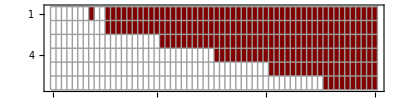

```mathematica
MatrixPlot[Y,ColorFunction->"Monochrome",AspectRatio->(1/4),Mesh-> All]
```

```mathematica
theFile=File["Yyyyy.txt"];
Export[theFile,Y//Chop];
```

### Standard way of deriving the equations of motion

Calculation of all 6 equations of motion

```mathematica
classicaleqs=DynamicEquations[tableUR10e@@q[t],CGtableUR10e,masslist,tensorlist,g0,q[t],qp[t],v[t],vp[t]];
```

We show just the first one...

```mathematica
classicaleqs[[1]];
```

### Equations of motion obtained multiplying the Dynamic Regressor and the List of Dynamic Parameters

Contestualmente alla creazione della lista di parametri (10 per ciascun link) i momenti di inerzia vengono scritti rispetto all'origine del frame di DH ancora in componenti nel frame di DH.

As we create the complete list with masses, first moments of inertia and second moments of inertia, we calculate the moments of inertia with respect to the local D-H frames, as indicated in the paper

```mathematica
paramlist=ExtractParameters[CGtableUR10e,masslist,tensorlist]//Simplify;paramlist
```

{m1,0,0,0,0,0,0,0,0,0,m2,-0.306 m2,0,0,0.,0.,0.,0.093636 m2,0.,0.093636 m2,m3,-0.28615 m3,0,0,0.,0.,0.,0.0818818 m3,0.,0.0818818 m3,m4,0,0.1719 m4,0,0.0295496 m4,0.,0.,0.,0.,0.0295496 m4,m5,0,-0.1149 m5,0,0.013202 m5,0.,0.,0.,0.,0.013202 m5,m6,0,0,-0.0922 m6,0.00850084 m6,0.,0.,0.00850084 m6,0.,0.}

Extract just the parameters for the first link...

```mathematica
paramlist[[1;;10]]
```

{m1,0,0,0,0,0,0,0,0,0}

Equations of motion with the regressor

```mathematica
regressoreqs=Y.paramlist;
```

### A little detour inside the package (just to show other useful functions)

Computation of the forward kinematics for the defined Denavit-Hartenberg table

```mathematica
FK= DHFKine[tableUR10e@@qsym]//FullSimplify
FK//Dimensions
```

{{Cos[q6] Sin[q1] Sin[q5]+Cos[q1] (Cos[q2+q3+q4] Cos[q5] Cos[q6]-Sin[q2+q3+q4] Sin[q6]),-Sin[q1] Sin[q5] Sin[q6]-Cos[q1] (Cos[q6] Sin[q2+q3+q4]+Cos[q2+q3+q4] Cos[q5] Sin[q6]),-Cos[q5] Sin[q1]+Cos[q1] Cos[q2+q3+q4] Sin[q5],-(dh22+dh32+dh42+dh62 Cos[q5]) Sin[q1]+Cos[q1] (dh21 Cos[q2]+dh31 Cos[q2+q3]-dh52 Sin[q2+q3+q4]+dh62 Cos[q2+q3+q4] Sin[q5])},{Cos[q2+q3+q4] Cos[q5] Cos[q6] Sin[q1]-Cos[q1] Cos[q6] Sin[q5]-Sin[q1] Sin[q2+q3+q4] Sin[q6],-Cos[q6] Sin[q1] Sin[q2+q3+q4]+(-Cos[q2+q3+q4] Cos[q5] Sin[q1]+Cos[q1] Sin[q5]) Sin[q6],Cos[q1] Cos[q5]+Cos[q2+q3+q4] Sin[q1] Sin[q5],Cos[q1] (dh22+dh32+dh42+dh62 Cos[q5])+Sin[q1] (dh21 Cos[q2]+dh31 Cos[q2+q3]-dh52 Sin[q2+q3+q4]+dh62 Cos[q2+q3+q4] Sin[q5])},{-Cos[q5] Cos[q6] Sin[q2+q3+q4]-Cos[q2+q3+q4] Sin[q6],-Cos[q2+q3+q4] Cos[q6]+Cos[q5] Sin[q2+q3+q4] Sin[q6],-Sin[q2+q3+q4] Sin[q5],dh12-dh52 Cos[q2+q3+q4]-dh21 Sin[q2]-dh31 Sin[q2+q3]-dh62 Sin[q2+q3+q4] Sin[q5]},{0,0,0,1}}

{4,4}

```mathematica
theFile=File["FK.txt"];
```

```mathematica
Export[theFile,FK];
```

Full Jacobian (classical for differntial kinematics)

```mathematica
JJ=DHJacob0[tableUR10e@@qsym]//FullSimplify
```

```mathematica
theFile=File["JJ.txt"];
Export[theFile,JJ];
```

```mathematica
D[JJ[q1_,q2_,q3_,q4_,q5_,q6_]=DHJacob0[tableUR10e@@q[t]]//FullSimplify,t]//FullSimplify
```

Derivata del jacobiano

```mathematica
theFile=File["DJJ.txt"];
Export[theFile,D[JJ[q1_,q2_,q3_,q4_,q5_,q6_]=DHJacob0[tableUR10e@@q[t]]//FullSimplify,t]//FullSimplify];
```

Set::write: Tag List in «1» is Protected.

Partial Jacobians (version for regressor dynamics) - reference points are still the origins of DH frames

For the first link

```mathematica
DHJacob0Dyn[tableUR10e@@qsym,1]//FullSimplify
```

For the second link

```mathematica
DHJacob0Dyn[tableUR10e@@qsym,2]//FullSimplify
```

Partial Jacobians (version for classical dynamics) - reference points are now the CGs of the link - a separate list must be supplied

First link

```mathematica
CGJacob0Dyn[tableUR10e@@qsym,CGtableUR10e,1]
```

Third link

```mathematica
CGJacob0Dyn[tableUR10e@@qsym,CGtableUR10e,3]
```

Inertia matrix

```mathematica
Bmat[q1_,q2_,q3_,q4_,q5_,q6_]=Inertia[tableUR10e@@qsym,CGtableUR10e,masslist,tensorlist]//Simplify
```

{{0.0956329 m2+0.230618 m3+0.351099 m4+0.377913 m5+0.384606 m6+(0.046818 m2+0.187272 m3+0.187272 m4+0.187272 m5+0.187272 m6) Cos[2 q2]+(0.175124 m3+0.350248 m4+0.350248 m5+0.350248 m6) Cos[q3]+0.0409409 m3 Cos[2 (q2+q3)]+0.163764 m4 Cos[2 (q2+q3)]+0.163764 m5 Cos[2 (q2+q3)]+0.163764 m6 Cos[2 (q2+q3)]+0.175124 m3 Cos[2 q2+q3]+0.350248 m4 Cos[2 q2+q3]+0.350248 m5 Cos[2 q2+q3]+0.350248 m6 Cos[2 q2+q3]-3.2×10^-7 m5 Cos[2 (q2+q3+q4)]-0.00669325 m6 Cos[2 (q2+q3+q4)]-0.00045784 m5 Sin[q4]-0.0662151 m6 Sin[q4]-0.0004896 m5 Sin[q3+q4]-0.0708084 m6 Sin[q3+q4]-0.0004896 m5 Sin[2 q2+q3+q4]-0.0708084 m6 Sin[2 q2+q3+q4]-0.00045784 m5 Sin[2 q2+2 q3+q4]-0.0662151 m6 Sin[2 q2+2 q3+q4],(0.000131153 m5+0.018968 m6) Cos[q2+q3+q4]+(0.0676079 m2+0.0300131 m3-0.00487091 m4+0.100332 m5+0.100332 m6) Sin[q2]+(0.0140331 m3-0.00455494 m4+0.0938234 m5+0.0938234 m6) Sin[q2+q3],(0.000131153 m5+0.018968 m6) Cos[q2+q3+q4]+(0.0140331 m3-0.00455494 m4+0.0938234 m5+0.0938234 m6) Sin[q2+q3],(0.000131153 m5+0.018968 m6) Cos[q2+q3+q4],0.,0.},{(0.000131153 m5+0.018968 m6) Cos[q2+q3+q4]+(0.0676079 m2+0.0300131 m3-0.00487091 m4+0.100332 m5+0.100332 m6) Sin[q2]+(0.0140331 m3-0.00455494 m4+0.0938234 m5+0.0938234 m6) Sin[q2+q3],0.093636 m2+0.456426 m3+0.702071 m4+0.702072 m5+0.715458 m6+(-0.0009792 m5-0.141617 m6) Cos[q4] Sin[q3]-0.00091568 m5 Sin[q4]-0.13243 m6 Sin[q4]+Cos[q3] (0.350248 m3+0.700495 m4+0.700495 m5+0.700495 m6+(-0.0009792 m5-0.141617 m6) Sin[q4]),0.0818818 m3+0.327527 m4+0.327528 m5+0.340914 m6+(-0.0004896 m5-0.0708084 m6) Cos[q4] Sin[q3]-0.00091568 m5 Sin[q4]-0.13243 m6 Sin[q4]+Cos[q3] (0.175124 m3+0.350248 m4+0.350248 m5+0.350248 m6+(-0.0004896 m5-0.0708084 m6) Sin[q4]),6.4×10^-7 m5+0.0133865 m6+(-0.0004896 m5-0.0708084 m6) Cos[q4] Sin[q3]+(-0.00045784 m5-0.0662151 m6-0.0004896 m5 Cos[q3]-0.0708084 m6 Cos[q3]) Sin[q4],0.,0.},{(0.000131153 m5+0.018968 m6) Cos[q2+q3+q4]+(0.0140331 m3-0.00455494 m4+0.0938234 m5+0.0938234 m6) Sin[q2+q3],0.0818818 m3+0.327527 m4+0.327528 m5+0.340914 m6+(-0.0004896 m5-0.0708084 m6) Cos[q4] Sin[q3]-0.00091568 m5 Sin[q4]-0.13243 m6 Sin[q4]+Cos[q3] (0.175124 m3+0.350248 m4+0.350248 m5+0.350248 m6+(-0.0004896 m5-0.0708084 m6) Sin[q4]),0.0818818 m3+0.327527 m4+0.327528 m5+0.340914 m6+(-0.00091568 m5-0.13243 m6) Sin[q4],6.4×10^-7 m5+0.0133865 m6+(-0.00045784 m5-0.0662151 m6) Sin[q4],0.,0.},{(0.000131153 m5+0.018968 m6) Cos[q2+q3+q4],6.4×10^-7 m5+0.0133865 m6+(-0.0004896 m5-0.0708084 m6) Cos[q4] Sin[q3]+(-0.00045784 m5-0.0662151 m6-0.0004896 m5 Cos[q3]-0.0708084 m6 Cos[q3]) Sin[q4],6.4×10^-7 m5+0.0133865 m6+(-0.00045784 m5-0.0662151 m6) Sin[q4],(6.4×10^-7+0. ⅈ) m5+(0.0133865+0. ⅈ) m6,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.}}

```mathematica
f=OpenWrite["B_regzz.m"]
```

```mathematica
WriteMatlab[Bmat[q1_,q2_,q3_,q4_,q5_,q6_]=Inertia[tableUR10e@@qsym,CGtableUR10e,masslist,tensorlist]//Simplify,f,"B",200]
```

```mathematica
Close[f]
```

B_regzz.m

```mathematica
theFile=File["B_reg_seconda_versione.txt"];
Export[theFile,Bmat[q1_,q2_,q3_,q4_,q5_,q6_]=Inertia[tableUR10e@@qsym,CGtableUR10e,masslist,tensorlist]//Simplify];
```

We map it of the time dependent joint vector

```mathematica
Bmat@@qsym
```

We check its symmetry!

```mathematica
Bmat@@qsym
```

{{0.0956329 m2+0.230618 m3+0.351099 m4+0.377913 m5+0.384606 m6+(0.046818 m2+0.187272 m3+0.187272 m4+0.187272 m5+0.187272 m6) Cos[2 q2]+(0.175124 m3+0.350248 m4+0.350248 m5+0.350248 m6) Cos[q3]+0.0409409 m3 Cos[2 (q2+q3)]+0.163764 m4 Cos[2 (q2+q3)]+0.163764 m5 Cos[2 (q2+q3)]+0.163764 m6 Cos[2 (q2+q3)]+0.175124 m3 Cos[2 q2+q3]+0.350248 m4 Cos[2 q2+q3]+0.350248 m5 Cos[2 q2+q3]+0.350248 m6 Cos[2 q2+q3]-3.2×10^-7 m5 Cos[2 (q2+q3+q4)]-0.00669325 m6 Cos[2 (q2+q3+q4)]-0.00045784 m5 Sin[q4]-0.0662151 m6 Sin[q4]-0.0004896 m5 Sin[q3+q4]-0.0708084 m6 Sin[q3+q4]-0.0004896 m5 Sin[2 q2+q3+q4]-0.0708084 m6 Sin[2 q2+q3+q4]-0.00045784 m5 Sin[2 q2+2 q3+q4]-0.0662151 m6 Sin[2 q2+2 q3+q4],(0.000131153 m5+0.018968 m6) Cos[q2+q3+q4]+(0.0676079 m2+0.0300131 m3-0.00487091 m4+0.100332 m5+0.100332 m6) Sin[q2]+(0.0140331 m3-0.00455494 m4+0.0938234 m5+0.0938234 m6) Sin[q2+q3],(0.000131153 m5+0.018968 m6) Cos[q2+q3+q4]+(0.0140331 m3-0.00455494 m4+0.0938234 m5+0.0938234 m6) Sin[q2+q3],(0.000131153 m5+0.018968 m6) Cos[q2+q3+q4],0.,0.},{(0.000131153 m5+0.018968 m6) Cos[q2+q3+q4]+(0.0676079 m2+0.0300131 m3-0.00487091 m4+0.100332 m5+0.100332 m6) Sin[q2]+(0.0140331 m3-0.00455494 m4+0.0938234 m5+0.0938234 m6) Sin[q2+q3],0.093636 m2+0.456426 m3+0.702071 m4+0.702072 m5+0.715458 m6+(-0.0009792 m5-0.141617 m6) Cos[q4] Sin[q3]-0.00091568 m5 Sin[q4]-0.13243 m6 Sin[q4]+Cos[q3] (0.350248 m3+0.700495 m4+0.700495 m5+0.700495 m6+(-0.0009792 m5-0.141617 m6) Sin[q4]),0.0818818 m3+0.327527 m4+0.327528 m5+0.340914 m6+(-0.0004896 m5-0.0708084 m6) Cos[q4] Sin[q3]-0.00091568 m5 Sin[q4]-0.13243 m6 Sin[q4]+Cos[q3] (0.175124 m3+0.350248 m4+0.350248 m5+0.350248 m6+(-0.0004896 m5-0.0708084 m6) Sin[q4]),6.4×10^-7 m5+0.0133865 m6+(-0.0004896 m5-0.0708084 m6) Cos[q4] Sin[q3]+(-0.00045784 m5-0.0662151 m6-0.0004896 m5 Cos[q3]-0.0708084 m6 Cos[q3]) Sin[q4],0.,0.},{(0.000131153 m5+0.018968 m6) Cos[q2+q3+q4]+(0.0140331 m3-0.00455494 m4+0.0938234 m5+0.0938234 m6) Sin[q2+q3],0.0818818 m3+0.327527 m4+0.327528 m5+0.340914 m6+(-0.0004896 m5-0.0708084 m6) Cos[q4] Sin[q3]-0.00091568 m5 Sin[q4]-0.13243 m6 Sin[q4]+Cos[q3] (0.175124 m3+0.350248 m4+0.350248 m5+0.350248 m6+(-0.0004896 m5-0.0708084 m6) Sin[q4]),0.0818818 m3+0.327527 m4+0.327528 m5+0.340914 m6+(-0.00091568 m5-0.13243 m6) Sin[q4],6.4×10^-7 m5+0.0133865 m6+(-0.00045784 m5-0.0662151 m6) Sin[q4],0.,0.},{(0.000131153 m5+0.018968 m6) Cos[q2+q3+q4],6.4×10^-7 m5+0.0133865 m6+(-0.0004896 m5-0.0708084 m6) Cos[q4] Sin[q3]+(-0.00045784 m5-0.0662151 m6-0.0004896 m5 Cos[q3]-0.0708084 m6 Cos[q3]) Sin[q4],6.4×10^-7 m5+0.0133865 m6+(-0.00045784 m5-0.0662151 m6) Sin[q4],(6.4×10^-7+0. ⅈ) m5+(0.0133865+0. ⅈ) m6,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.}}

```mathematica
(*Bmat@@qsym-Transpose[Bmat@@qsym]//Simplify*)
```

We compute the Coriolis matrix derived from the Christoffel symbols

```mathematica
Cmat=InertiaToCoriolis[Bmat@@q[t],q[t],qp[t]];
```

Part::partd: Part specification Bmat[t]⟦1,1⟧ is longer than depth of object.

Part::pkspec1: The expression #2 cannot be used as a part specification.

Part::partd: Part specification Bmat[t]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
Cmat[1]
```

```mathematica
Cmat = Simplify[Cmat,TimeConstraint->0.1]//Timing
```

```mathematica
Cmat=Cmat//Chop;
```

```mathematica
Cmat = Cmat//Simplify;
```

$Aborted

```mathematica
theFile=File["C_reg2.txt"];
Export[theFile,Cmat];
```

```mathematica
fsf=OpenWrite["C_regzbbbz.m"]
```

```mathematica
WriteMatlab[Cmat,fsf,"C",200];
```

```mathematica
Close[fsf]
```

C_regzbbbz.m

```mathematica
Gvec=Gravitational[tableUR10e@@qsym,CGtableUR10e,masslist,g0]//Simplify
```

{-m1 {{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m2 {{-0.220941 Cos[q1]-0.306 Cos[q2] Sin[q1],0.306 Cos[q1] Cos[q2]-0.220941 Sin[q1],0.},{-0.306 Cos[q1] Sin[q2],-0.306 Sin[q1] Sin[q2],-0.306 Cos[q2]},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m3 {{-0.049041 Cos[q1]+Sin[q1] (Cos[q2] (-0.612-0.28615 Cos[q3])+0.28615 Sin[q2] Sin[q3]),-0.049041 Sin[q1]+Cos[q1] (Cos[q2] (0.612+0.28615 Cos[q3])-0.28615 Sin[q2] Sin[q3]),0.},{Cos[q1] ((-0.612-0.28615 Cos[q3]) Sin[q2]-0.28615 Cos[q2] Sin[q3]),Sin[q1] ((-0.612-0.28615 Cos[q3]) Sin[q2]-0.28615 Cos[q2] Sin[q3]),Cos[q2] (-0.612-0.28615 Cos[q3])+0.28615 Sin[q2] Sin[q3]},{Cos[q1] (-0.28615 Cos[q3] Sin[q2]-0.28615 Cos[q2] Sin[q3]),Sin[q1] (-0.28615 Cos[q3] Sin[q2]-0.28615 Cos[q2] Sin[q3]),-0.28615 Cos[q2] Cos[q3]+0.28615 Sin[q2] Sin[q3]},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m4 {{0.007959 Cos[q1]+Sin[q1] (Cos[q2] (-0.612-0.5723 Cos[q3])+0.5723 Sin[q2] Sin[q3]),0.007959 Sin[q1]+Cos[q1] (Cos[q2] (0.612+0.5723 Cos[q3])-0.5723 Sin[q2] Sin[q3]),0.},{-0.5723 Cos[q1] ((1.06937+1. Cos[q3]) Sin[q2]+1. Cos[q2] Sin[q3]),-0.5723 Sin[q1] ((1.06937+1. Cos[q3]) Sin[q2]+1. Cos[q2] Sin[q3]),Cos[q2] (-0.612-0.5723 Cos[q3])+0.5723 Sin[q2] Sin[q3]},{Cos[q1] (-0.5723 Cos[q3] Sin[q2]-0.5723 Cos[q2] Sin[q3]),Sin[q1] (-0.5723 Cos[q3] Sin[q2]-0.5723 Cos[q2] Sin[q3]),-0.5723 Cos[q2] Cos[q3]+0.5723 Sin[q2] Sin[q3]},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m5 {{-0.163941 Cos[q1]+Sin[q1] (-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.0008 Sin[q2+q3+q4]),-0.163941 Sin[q1]+Cos[q1] (0.612 Cos[q2]+0.5723 Cos[q2+q3]-0.0008 Sin[q2+q3+q4]),0.},{Cos[q1] (-0.0008 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),Sin[q1] (-0.0008 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.0008 Sin[q2+q3+q4]},{Cos[q1] (-0.0008 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),Sin[q1] (-0.0008 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),-0.5723 Cos[q2+q3]+0.0008 Sin[q2+q3+q4]},{-0.0008 Cos[q1] Cos[q2+q3+q4],-0.0008 Cos[q2+q3+q4] Sin[q1],0.0008 Sin[q2+q3+q4]},{0.,0.,0.},{0.,0.,0.}}.g0-m6 {{-0.163941 Cos[q1]+Sin[q1] (-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.1157 Sin[q2+q3+q4]),-0.163941 Sin[q1]+Cos[q1] (0.612 Cos[q2]+0.5723 Cos[q2+q3]-0.1157 Sin[q2+q3+q4]),0.},{Cos[q1] (-0.1157 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),Sin[q1] (-0.1157 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.1157 Sin[q2+q3+q4]},{Cos[q1] (-0.1157 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),Sin[q1] (-0.1157 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),-0.5723 Cos[q2+q3]+0.1157 Sin[q2+q3+q4]},{-0.1157 Cos[q1] Cos[q2+q3+q4],-0.1157 Cos[q2+q3+q4] Sin[q1],0.1157 Sin[q2+q3+q4]},{0.,0.,0.},{0.,0.,0.}}.g0,-m1 {{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m2 {{-0.220941 Cos[q1]-0.306 Cos[q2] Sin[q1],0.306 Cos[q1] Cos[q2]-0.220941 Sin[q1],0.},{-0.306 Cos[q1] Sin[q2],-0.306 Sin[q1] Sin[q2],-0.306 Cos[q2]},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m3 {{-0.049041 Cos[q1]+Sin[q1] (Cos[q2] (-0.612-0.28615 Cos[q3])+0.28615 Sin[q2] Sin[q3]),-0.049041 Sin[q1]+Cos[q1] (Cos[q2] (0.612+0.28615 Cos[q3])-0.28615 Sin[q2] Sin[q3]),0.},{Cos[q1] ((-0.612-0.28615 Cos[q3]) Sin[q2]-0.28615 Cos[q2] Sin[q3]),Sin[q1] ((-0.612-0.28615 Cos[q3]) Sin[q2]-0.28615 Cos[q2] Sin[q3]),Cos[q2] (-0.612-0.28615 Cos[q3])+0.28615 Sin[q2] Sin[q3]},{Cos[q1] (-0.28615 Cos[q3] Sin[q2]-0.28615 Cos[q2] Sin[q3]),Sin[q1] (-0.28615 Cos[q3] Sin[q2]-0.28615 Cos[q2] Sin[q3]),-0.28615 Cos[q2] Cos[q3]+0.28615 Sin[q2] Sin[q3]},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m4 {{0.007959 Cos[q1]+Sin[q1] (Cos[q2] (-0.612-0.5723 Cos[q3])+0.5723 Sin[q2] Sin[q3]),0.007959 Sin[q1]+Cos[q1] (Cos[q2] (0.612+0.5723 Cos[q3])-0.5723 Sin[q2] Sin[q3]),0.},{-0.5723 Cos[q1] ((1.06937+1. Cos[q3]) Sin[q2]+1. Cos[q2] Sin[q3]),-0.5723 Sin[q1] ((1.06937+1. Cos[q3]) Sin[q2]+1. Cos[q2] Sin[q3]),Cos[q2] (-0.612-0.5723 Cos[q3])+0.5723 Sin[q2] Sin[q3]},{Cos[q1] (-0.5723 Cos[q3] Sin[q2]-0.5723 Cos[q2] Sin[q3]),Sin[q1] (-0.5723 Cos[q3] Sin[q2]-0.5723 Cos[q2] Sin[q3]),-0.5723 Cos[q2] Cos[q3]+0.5723 Sin[q2] Sin[q3]},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m5 {{-0.163941 Cos[q1]+Sin[q1] (-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.0008 Sin[q2+q3+q4]),-0.163941 Sin[q1]+Cos[q1] (0.612 Cos[q2]+0.5723 Cos[q2+q3]-0.0008 Sin[q2+q3+q4]),0.},{Cos[q1] (-0.0008 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),Sin[q1] (-0.0008 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.0008 Sin[q2+q3+q4]},{Cos[q1] (-0.0008 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),Sin[q1] (-0.0008 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),-0.5723 Cos[q2+q3]+0.0008 Sin[q2+q3+q4]},{-0.0008 Cos[q1] Cos[q2+q3+q4],-0.0008 Cos[q2+q3+q4] Sin[q1],0.0008 Sin[q2+q3+q4]},{0.,0.,0.},{0.,0.,0.}}.g0-m6 {{-0.163941 Cos[q1]+Sin[q1] (-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.1157 Sin[q2+q3+q4]),-0.163941 Sin[q1]+Cos[q1] (0.612 Cos[q2]+0.5723 Cos[q2+q3]-0.1157 Sin[q2+q3+q4]),0.},{Cos[q1] (-0.1157 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),Sin[q1] (-0.1157 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.1157 Sin[q2+q3+q4]},{Cos[q1] (-0.1157 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),Sin[q1] (-0.1157 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),-0.5723 Cos[q2+q3]+0.1157 Sin[q2+q3+q4]},{-0.1157 Cos[q1] Cos[q2+q3+q4],-0.1157 Cos[q2+q3+q4] Sin[q1],0.1157 Sin[q2+q3+q4]},{0.,0.,0.},{0.,0.,0.}}.g0,-m1 {{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m2 {{-0.220941 Cos[q1]-0.306 Cos[q2] Sin[q1],0.306 Cos[q1] Cos[q2]-0.220941 Sin[q1],0.},{-0.306 Cos[q1] Sin[q2],-0.306 Sin[q1] Sin[q2],-0.306 Cos[q2]},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m3 {{-0.049041 Cos[q1]+Sin[q1] (Cos[q2] (-0.612-0.28615 Cos[q3])+0.28615 Sin[q2] Sin[q3]),-0.049041 Sin[q1]+Cos[q1] (Cos[q2] (0.612+0.28615 Cos[q3])-0.28615 Sin[q2] Sin[q3]),0.},{Cos[q1] ((-0.612-0.28615 Cos[q3]) Sin[q2]-0.28615 Cos[q2] Sin[q3]),Sin[q1] ((-0.612-0.28615 Cos[q3]) Sin[q2]-0.28615 Cos[q2] Sin[q3]),Cos[q2] (-0.612-0.28615 Cos[q3])+0.28615 Sin[q2] Sin[q3]},{Cos[q1] (-0.28615 Cos[q3] Sin[q2]-0.28615 Cos[q2] Sin[q3]),Sin[q1] (-0.28615 Cos[q3] Sin[q2]-0.28615 Cos[q2] Sin[q3]),-0.28615 Cos[q2] Cos[q3]+0.28615 Sin[q2] Sin[q3]},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m4 {{0.007959 Cos[q1]+Sin[q1] (Cos[q2] (-0.612-0.5723 Cos[q3])+0.5723 Sin[q2] Sin[q3]),0.007959 Sin[q1]+Cos[q1] (Cos[q2] (0.612+0.5723 Cos[q3])-0.5723 Sin[q2] Sin[q3]),0.},{-0.5723 Cos[q1] ((1.06937+1. Cos[q3]) Sin[q2]+1. Cos[q2] Sin[q3]),-0.5723 Sin[q1] ((1.06937+1. Cos[q3]) Sin[q2]+1. Cos[q2] Sin[q3]),Cos[q2] (-0.612-0.5723 Cos[q3])+0.5723 Sin[q2] Sin[q3]},{Cos[q1] (-0.5723 Cos[q3] Sin[q2]-0.5723 Cos[q2] Sin[q3]),Sin[q1] (-0.5723 Cos[q3] Sin[q2]-0.5723 Cos[q2] Sin[q3]),-0.5723 Cos[q2] Cos[q3]+0.5723 Sin[q2] Sin[q3]},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m5 {{-0.163941 Cos[q1]+Sin[q1] (-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.0008 Sin[q2+q3+q4]),-0.163941 Sin[q1]+Cos[q1] (0.612 Cos[q2]+0.5723 Cos[q2+q3]-0.0008 Sin[q2+q3+q4]),0.},{Cos[q1] (-0.0008 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),Sin[q1] (-0.0008 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.0008 Sin[q2+q3+q4]},{Cos[q1] (-0.0008 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),Sin[q1] (-0.0008 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),-0.5723 Cos[q2+q3]+0.0008 Sin[q2+q3+q4]},{-0.0008 Cos[q1] Cos[q2+q3+q4],-0.0008 Cos[q2+q3+q4] Sin[q1],0.0008 Sin[q2+q3+q4]},{0.,0.,0.},{0.,0.,0.}}.g0-m6 {{-0.163941 Cos[q1]+Sin[q1] (-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.1157 Sin[q2+q3+q4]),-0.163941 Sin[q1]+Cos[q1] (0.612 Cos[q2]+0.5723 Cos[q2+q3]-0.1157 Sin[q2+q3+q4]),0.},{Cos[q1] (-0.1157 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),Sin[q1] (-0.1157 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.1157 Sin[q2+q3+q4]},{Cos[q1] (-0.1157 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),Sin[q1] (-0.1157 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),-0.5723 Cos[q2+q3]+0.1157 Sin[q2+q3+q4]},{-0.1157 Cos[q1] Cos[q2+q3+q4],-0.1157 Cos[q2+q3+q4] Sin[q1],0.1157 Sin[q2+q3+q4]},{0.,0.,0.},{0.,0.,0.}}.g0,-m1 {{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m2 {{-0.220941 Cos[q1]-0.306 Cos[q2] Sin[q1],0.306 Cos[q1] Cos[q2]-0.220941 Sin[q1],0.},{-0.306 Cos[q1] Sin[q2],-0.306 Sin[q1] Sin[q2],-0.306 Cos[q2]},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m3 {{-0.049041 Cos[q1]+Sin[q1] (Cos[q2] (-0.612-0.28615 Cos[q3])+0.28615 Sin[q2] Sin[q3]),-0.049041 Sin[q1]+Cos[q1] (Cos[q2] (0.612+0.28615 Cos[q3])-0.28615 Sin[q2] Sin[q3]),0.},{Cos[q1] ((-0.612-0.28615 Cos[q3]) Sin[q2]-0.28615 Cos[q2] Sin[q3]),Sin[q1] ((-0.612-0.28615 Cos[q3]) Sin[q2]-0.28615 Cos[q2] Sin[q3]),Cos[q2] (-0.612-0.28615 Cos[q3])+0.28615 Sin[q2] Sin[q3]},{Cos[q1] (-0.28615 Cos[q3] Sin[q2]-0.28615 Cos[q2] Sin[q3]),Sin[q1] (-0.28615 Cos[q3] Sin[q2]-0.28615 Cos[q2] Sin[q3]),-0.28615 Cos[q2] Cos[q3]+0.28615 Sin[q2] Sin[q3]},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m4 {{0.007959 Cos[q1]+Sin[q1] (Cos[q2] (-0.612-0.5723 Cos[q3])+0.5723 Sin[q2] Sin[q3]),0.007959 Sin[q1]+Cos[q1] (Cos[q2] (0.612+0.5723 Cos[q3])-0.5723 Sin[q2] Sin[q3]),0.},{-0.5723 Cos[q1] ((1.06937+1. Cos[q3]) Sin[q2]+1. Cos[q2] Sin[q3]),-0.5723 Sin[q1] ((1.06937+1. Cos[q3]) Sin[q2]+1. Cos[q2] Sin[q3]),Cos[q2] (-0.612-0.5723 Cos[q3])+0.5723 Sin[q2] Sin[q3]},{Cos[q1] (-0.5723 Cos[q3] Sin[q2]-0.5723 Cos[q2] Sin[q3]),Sin[q1] (-0.5723 Cos[q3] Sin[q2]-0.5723 Cos[q2] Sin[q3]),-0.5723 Cos[q2] Cos[q3]+0.5723 Sin[q2] Sin[q3]},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m5 {{-0.163941 Cos[q1]+Sin[q1] (-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.0008 Sin[q2+q3+q4]),-0.163941 Sin[q1]+Cos[q1] (0.612 Cos[q2]+0.5723 Cos[q2+q3]-0.0008 Sin[q2+q3+q4]),0.},{Cos[q1] (-0.0008 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),Sin[q1] (-0.0008 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.0008 Sin[q2+q3+q4]},{Cos[q1] (-0.0008 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),Sin[q1] (-0.0008 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),-0.5723 Cos[q2+q3]+0.0008 Sin[q2+q3+q4]},{-0.0008 Cos[q1] Cos[q2+q3+q4],-0.0008 Cos[q2+q3+q4] Sin[q1],0.0008 Sin[q2+q3+q4]},{0.,0.,0.},{0.,0.,0.}}.g0-m6 {{-0.163941 Cos[q1]+Sin[q1] (-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.1157 Sin[q2+q3+q4]),-0.163941 Sin[q1]+Cos[q1] (0.612 Cos[q2]+0.5723 Cos[q2+q3]-0.1157 Sin[q2+q3+q4]),0.},{Cos[q1] (-0.1157 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),Sin[q1] (-0.1157 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.1157 Sin[q2+q3+q4]},{Cos[q1] (-0.1157 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),Sin[q1] (-0.1157 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),-0.5723 Cos[q2+q3]+0.1157 Sin[q2+q3+q4]},{-0.1157 Cos[q1] Cos[q2+q3+q4],-0.1157 Cos[q2+q3+q4] Sin[q1],0.1157 Sin[q2+q3+q4]},{0.,0.,0.},{0.,0.,0.}}.g0,-m1 {{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m2 {{-0.220941 Cos[q1]-0.306 Cos[q2] Sin[q1],0.306 Cos[q1] Cos[q2]-0.220941 Sin[q1],0.},{-0.306 Cos[q1] Sin[q2],-0.306 Sin[q1] Sin[q2],-0.306 Cos[q2]},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m3 {{-0.049041 Cos[q1]+Sin[q1] (Cos[q2] (-0.612-0.28615 Cos[q3])+0.28615 Sin[q2] Sin[q3]),-0.049041 Sin[q1]+Cos[q1] (Cos[q2] (0.612+0.28615 Cos[q3])-0.28615 Sin[q2] Sin[q3]),0.},{Cos[q1] ((-0.612-0.28615 Cos[q3]) Sin[q2]-0.28615 Cos[q2] Sin[q3]),Sin[q1] ((-0.612-0.28615 Cos[q3]) Sin[q2]-0.28615 Cos[q2] Sin[q3]),Cos[q2] (-0.612-0.28615 Cos[q3])+0.28615 Sin[q2] Sin[q3]},{Cos[q1] (-0.28615 Cos[q3] Sin[q2]-0.28615 Cos[q2] Sin[q3]),Sin[q1] (-0.28615 Cos[q3] Sin[q2]-0.28615 Cos[q2] Sin[q3]),-0.28615 Cos[q2] Cos[q3]+0.28615 Sin[q2] Sin[q3]},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m4 {{0.007959 Cos[q1]+Sin[q1] (Cos[q2] (-0.612-0.5723 Cos[q3])+0.5723 Sin[q2] Sin[q3]),0.007959 Sin[q1]+Cos[q1] (Cos[q2] (0.612+0.5723 Cos[q3])-0.5723 Sin[q2] Sin[q3]),0.},{-0.5723 Cos[q1] ((1.06937+1. Cos[q3]) Sin[q2]+1. Cos[q2] Sin[q3]),-0.5723 Sin[q1] ((1.06937+1. Cos[q3]) Sin[q2]+1. Cos[q2] Sin[q3]),Cos[q2] (-0.612-0.5723 Cos[q3])+0.5723 Sin[q2] Sin[q3]},{Cos[q1] (-0.5723 Cos[q3] Sin[q2]-0.5723 Cos[q2] Sin[q3]),Sin[q1] (-0.5723 Cos[q3] Sin[q2]-0.5723 Cos[q2] Sin[q3]),-0.5723 Cos[q2] Cos[q3]+0.5723 Sin[q2] Sin[q3]},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m5 {{-0.163941 Cos[q1]+Sin[q1] (-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.0008 Sin[q2+q3+q4]),-0.163941 Sin[q1]+Cos[q1] (0.612 Cos[q2]+0.5723 Cos[q2+q3]-0.0008 Sin[q2+q3+q4]),0.},{Cos[q1] (-0.0008 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),Sin[q1] (-0.0008 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.0008 Sin[q2+q3+q4]},{Cos[q1] (-0.0008 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),Sin[q1] (-0.0008 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),-0.5723 Cos[q2+q3]+0.0008 Sin[q2+q3+q4]},{-0.0008 Cos[q1] Cos[q2+q3+q4],-0.0008 Cos[q2+q3+q4] Sin[q1],0.0008 Sin[q2+q3+q4]},{0.,0.,0.},{0.,0.,0.}}.g0-m6 {{-0.163941 Cos[q1]+Sin[q1] (-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.1157 Sin[q2+q3+q4]),-0.163941 Sin[q1]+Cos[q1] (0.612 Cos[q2]+0.5723 Cos[q2+q3]-0.1157 Sin[q2+q3+q4]),0.},{Cos[q1] (-0.1157 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),Sin[q1] (-0.1157 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.1157 Sin[q2+q3+q4]},{Cos[q1] (-0.1157 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),Sin[q1] (-0.1157 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),-0.5723 Cos[q2+q3]+0.1157 Sin[q2+q3+q4]},{-0.1157 Cos[q1] Cos[q2+q3+q4],-0.1157 Cos[q2+q3+q4] Sin[q1],0.1157 Sin[q2+q3+q4]},{0.,0.,0.},{0.,0.,0.}}.g0,-m1 {{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m2 {{-0.220941 Cos[q1]-0.306 Cos[q2] Sin[q1],0.306 Cos[q1] Cos[q2]-0.220941 Sin[q1],0.},{-0.306 Cos[q1] Sin[q2],-0.306 Sin[q1] Sin[q2],-0.306 Cos[q2]},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m3 {{-0.049041 Cos[q1]+Sin[q1] (Cos[q2] (-0.612-0.28615 Cos[q3])+0.28615 Sin[q2] Sin[q3]),-0.049041 Sin[q1]+Cos[q1] (Cos[q2] (0.612+0.28615 Cos[q3])-0.28615 Sin[q2] Sin[q3]),0.},{Cos[q1] ((-0.612-0.28615 Cos[q3]) Sin[q2]-0.28615 Cos[q2] Sin[q3]),Sin[q1] ((-0.612-0.28615 Cos[q3]) Sin[q2]-0.28615 Cos[q2] Sin[q3]),Cos[q2] (-0.612-0.28615 Cos[q3])+0.28615 Sin[q2] Sin[q3]},{Cos[q1] (-0.28615 Cos[q3] Sin[q2]-0.28615 Cos[q2] Sin[q3]),Sin[q1] (-0.28615 Cos[q3] Sin[q2]-0.28615 Cos[q2] Sin[q3]),-0.28615 Cos[q2] Cos[q3]+0.28615 Sin[q2] Sin[q3]},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m4 {{0.007959 Cos[q1]+Sin[q1] (Cos[q2] (-0.612-0.5723 Cos[q3])+0.5723 Sin[q2] Sin[q3]),0.007959 Sin[q1]+Cos[q1] (Cos[q2] (0.612+0.5723 Cos[q3])-0.5723 Sin[q2] Sin[q3]),0.},{-0.5723 Cos[q1] ((1.06937+1. Cos[q3]) Sin[q2]+1. Cos[q2] Sin[q3]),-0.5723 Sin[q1] ((1.06937+1. Cos[q3]) Sin[q2]+1. Cos[q2] Sin[q3]),Cos[q2] (-0.612-0.5723 Cos[q3])+0.5723 Sin[q2] Sin[q3]},{Cos[q1] (-0.5723 Cos[q3] Sin[q2]-0.5723 Cos[q2] Sin[q3]),Sin[q1] (-0.5723 Cos[q3] Sin[q2]-0.5723 Cos[q2] Sin[q3]),-0.5723 Cos[q2] Cos[q3]+0.5723 Sin[q2] Sin[q3]},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}.g0-m5 {{-0.163941 Cos[q1]+Sin[q1] (-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.0008 Sin[q2+q3+q4]),-0.163941 Sin[q1]+Cos[q1] (0.612 Cos[q2]+0.5723 Cos[q2+q3]-0.0008 Sin[q2+q3+q4]),0.},{Cos[q1] (-0.0008 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),Sin[q1] (-0.0008 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.0008 Sin[q2+q3+q4]},{Cos[q1] (-0.0008 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),Sin[q1] (-0.0008 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),-0.5723 Cos[q2+q3]+0.0008 Sin[q2+q3+q4]},{-0.0008 Cos[q1] Cos[q2+q3+q4],-0.0008 Cos[q2+q3+q4] Sin[q1],0.0008 Sin[q2+q3+q4]},{0.,0.,0.},{0.,0.,0.}}.g0-m6 {{-0.163941 Cos[q1]+Sin[q1] (-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.1157 Sin[q2+q3+q4]),-0.163941 Sin[q1]+Cos[q1] (0.612 Cos[q2]+0.5723 Cos[q2+q3]-0.1157 Sin[q2+q3+q4]),0.},{Cos[q1] (-0.1157 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),Sin[q1] (-0.1157 Cos[q2+q3+q4]-0.612 Sin[q2]-0.5723 Sin[q2+q3]),-0.612 Cos[q2]-0.5723 Cos[q2+q3]+0.1157 Sin[q2+q3+q4]},{Cos[q1] (-0.1157 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),Sin[q1] (-0.1157 Cos[q2+q3+q4]-0.5723 Sin[q2+q3]),-0.5723 Cos[q2+q3]+0.1157 Sin[q2+q3+q4]},{-0.1157 Cos[q1] Cos[q2+q3+q4],-0.1157 Cos[q2+q3+q4] Sin[q1],0.1157 Sin[q2+q3+q4]},{0.,0.,0.},{0.,0.,0.}}.g0}

```mathematica
theFile=File["G_reg2.txt"];
Export[theFile,Gvec];
```

```mathematica
Gvec[[6]]//Simplify
```

0.